# Numerical Solutions to Volterra Equations of the Second Kind

Version 1.30
copyright © 2002-Year Michael Honeychurch

Reference: Nicholson, R.S.and M.L.Olmstead, (1972). Numerical solution of integral equations. In Electrochemistry; Calculations, Simulations, and Instrumentation, (eds. J.S. Mattson, H.B. Mark jnr., H.C. MacDonald jnr.), pp.119-138, Marcel Dekker, New York.

In this notebook you are asked to load data from the SERM/Data folder. To prepare for this copy the line below to an input cell, replace the file path with the file path for the "Data" folder on your computer and press ⌤

```mathematica
AppendTo[$Path,"(*path to SERM *)/SERM/Data/DigiSimdata"];
```

## Mathematica Preliminaries

```mathematica
SetDirectory["/Users/mikehoneychurch/SERM/Data/DigiSimdata"]
```

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
Background->Automatic,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],,AbsoluteThickness[.7]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
cvTicks1[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],2.5}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-2.5}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.5}]];

cvTicks2[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],.1}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-.1}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.02}]];

cvTicks3[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],2.5}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-2.5}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.5}]];

cvTicks4[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],.1}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-.1}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.02}]];
```

```mathematica
optionC={
PlotStyle-> {Blue,AbsoluteThickness[0.7]},
FrameTicks:>  {cvTicks1,cvTicks2,cvTicks3,cvTicks4},
FrameLabel->{
Style["αnF/RT(E-E°)",FontFamily-> "Times New Roman",FontColor-> Black,FontSlant-> Italic,FontSize-> 12],Style["χ",FontFamily-> "Times New Roman",FontSlant-> Italic,FontColor->Black,FontSize-> 12],
None,
None}};
```

```mathematica
optionD={
FrameTicks->  Automatic,
PlotStyle-> {{Blue,AbsoluteThickness[0.7]},{Red,AbsoluteThickness[0.7]}},
FrameLabel->{
Style["αnF/RT(E-E°)",FontFamily-> "Times New Roman",FontColor-> Black,FontSlant-> Italic,FontSize-> 12],Style["χ",FontFamily-> "Times New Roman",FontSlant-> Italic,FontColor->Black,FontSize-> 12],
None,
None}};
```

```mathematica
Clear[LowerDiagonalMatrix];

LowerDiagonalMatrix[f_,n_Integer?NonNegative]:=Array[If[#>=#2,f[##],0]&,{n,n}]
```

```mathematica
$Line=0;
```

## Huber's Method

### Procedural Implementation of Huber's Method for Irreversible Cyclic Voltammetry

\[FreakedSmiley]THIS IS SLOW

```mathematica
Clear[n,Δe,ks,α,𝒟,F,R,T,v,ki,g,hi,a,f];

n=450;(*number of potential steps*)

Δe=0.1;(*dimensionless potential increment*)

ks=10^-5(*standard rate constant*);

α=0.5(*transfer coefficient*);

𝒟=10^-5(*diffusion coefficient*);

F=96485.(*Faradays constant*);

R=8.3144(*gas constant*);

T=298.(*temperature*);

v=1;(*sweep rate*)

ki=ks*Exp[-α*10];

g:=Sqrt[Pi*α*F/(R*T)*v*𝒟]*Exp[-m*α*Δe]/ki;

h1=0.75*(α*Δe)^(3/2);

a=Table[0.,{n}];

χ=Table[0.,{n}];

For[m=1,m<n+1,m++,a⟦m⟧=1/((g*α*Δe)+h1)*(1-(h1*∑_(i=1)^(m-1) a⟦i⟧*((m-i+1)^(3/2)-(m-i)^(3/2)))-((g*α*Δe)*∑_(i=1)^(m-1) a⟦i⟧))]

χ⟦1⟧=(α*Δe*a⟦1⟧);

For[m=2,m<n+1,m++,χ⟦m⟧=(α*Δe*a⟦m⟧)+χ⟦m-1⟧]

result=Table[{(10-(α*m*Δe)),-χ⟦m⟧},{m,1,n}];
```

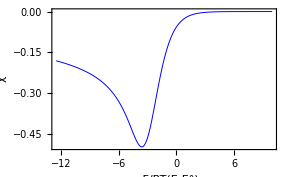

```mathematica
ListPlot[result,optionC]
```

### Functional Implementation of Huber's Method for Irreversible Cyclic Voltammetry

```mathematica
Clear[Δe,n,ks,α,𝒟,F,R,T,v,ki,init,h1,list,list2,g,a,f,mat,mat2,result];

n=400;(*number of potential steps*)

Δe=0.4;(*dimensionless potential increment*)

ks=1.*^-6(*standard rate constant*);

α=0.5(*transfer coefficient*);

𝒟=1.*^-5(*diffusion coefficient*);

F=96485.(*Faradays constant*);

R=8.3144(*gas constant*);

T=298.(*temperature*);

v=1.;(*sweep rate*)

init=10.(*initial dimensionless potential*);

ki=ks*Exp[-α*init];

h1=0.75*(α*Δe)^(3/2);


list=Table[((n-i+1)^(3/2)-(n-i)^(3/2))//N,{i,n,1,-1}];

x[r_,s_]:=h1*list⟦r-s+1⟧;

mat=LowerDiagonalMatrix[x,n];


list2=Table[α*Δe*Sqrt[Pi*α*F/(R*T)*v*𝒟]*Exp[-i*α*Δe]/ki,{i,n}];

g[r_,_]:=list2⟦r⟧;

mat2=LowerDiagonalMatrix[g,n];


a=LinearSolve[mat+mat2,Table[1.,{n}]];

f=Table[0.,{n}];

f⟦1⟧=(α*Δe*a⟦1⟧);

result=Map[{(init-#*Δe),-Set[f⟦#⟧,(α*Δe*a⟦#⟧)+f⟦#-1⟧]}&,Range[2,n]];
```

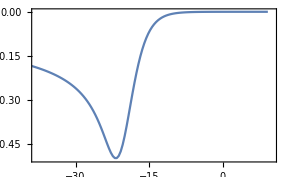

```mathematica
ListPlot[result,PlotRange-> {{-38,10}, {0, -0.5}}]
```

### Procedural Implementation of Huber's Method for Quasi-reversible Cyclic Voltammetry

\[FreakedSmiley]THIS IS SLOW

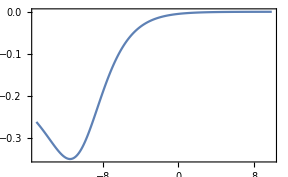

```mathematica
Clear[n,Δe,ks,v,α,𝒟,F,R,T,g,hi,c1,c2,a,f];


n=200;(*number of potential steps*)

Δe=0.125;(*dimensionless potential increment*)

ks=1.*^-4(*standard rate constant*);

v=1.;(*sweep rate*)

α=0.5(*transfer coefficient*);

𝒟=1.*^-5(*diffusion coefficient*);

F=96485.(*Faradays constant*);

R=8.3144(*gas constant*);

T=298.(*temperature*);

ψ=ks/Sqrt[Pi*F/(R*T)*v*𝒟];

g:=Exp[-m*Δe];

h1=4*(Δe)^(3/2)/3;

c1=Exp[α*10.]/ψ;

c2=Exp[10.];

a=Table[0.,{n}];

χ=Table[0.,{n}];


For[m=1,m<n+1,m++,a⟦m⟧=1/((c1*g^α*Δe)+h1+(c2*g*h1))*(1-((1+c2*g)*h1*∑_(i=1)^(m-1) a⟦i⟧*((m-i+1)^(3/2)-(m-i)^(3/2)))-((c1*g^α*Δe)*∑_(i=1)^(m-1) a⟦i⟧))]

χ⟦1⟧=(Δe*a⟦1⟧);

For[m=2,m<n+1,m++,χ⟦m⟧=(Δe*a⟦m⟧)+χ⟦m-1⟧]

result=Table[{(10.-(m*Δe)),-Sqrt[Pi]*χ⟦m⟧},{m,1,n}];

plot1=ListPlot[result]
```

### Functional Implementation of Huber's Method for Quasi-reversible Cyclic Voltammetry-incomplete

```mathematica
Clear[Δe,n,ks,α,𝒟,F,R,T,v,init,h1,v1,v2,list,list2,g,g1,a,f,mat,mat2,result];

n=200;(*number of potential steps*)

Δe=0.2;(*dimensionless potential increment*)

ks=1.*^-4(*standard rate constant*);

α=0.5(*transfer coefficient*);

𝒟=1.*^-5(*diffusion coefficient*);

F=96485.(*Faradays constant*);

R=8.3144(*gas constant*);

T=298.(*temperature*);

v=1.;(*sweep rate*)

init=10.(*initial dimensionless potential*);

ψ=ks/Sqrt[Pi*F/(R*T)*v*𝒟];

c1=Exp[α*10.]/ψ;

c2=Exp[10.];

h1=4*(Δe)^(3/2)/3;

list=Table[((n-i+1)^(3/2)-(n-i)^(3/2))//N,{i,n,1,-1}];
Set[list⟦1⟧,0];

list2=Table[Exp[-i*Δe],{i,n}];

x[r_,s_]:=list⟦r-s+1⟧;
g1[r_,_]:=Sqrt[list2⟦r⟧];
g[r_]:=list2⟦r⟧;

v1=Table[1.,{n}];
v2=(1+c2*Array[g,n])*h1;

mat=v2*LowerDiagonalMatrix[x,n];

mat2=c1*Δe*LowerDiagonalMatrix[g1,n];

Table[Set[mat2⟦i,i⟧,mat2⟦i,i⟧+h1+c2*h1*g[i]],{i,1,n}];
a=-Sqrt[Pi]*LinearSolve[mat+mat2,v1];

χ=Table[0.,{n}];

χ⟦1⟧=(Δe*a⟦1⟧);

result=Map[{(init-#*Δe),Set[χ⟦#⟧,(Δe*a⟦#⟧)+χ⟦#-1⟧]}&,Range[2,n]];
```

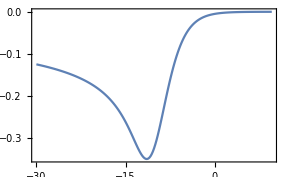

```mathematica
plot2=ListPlot[result]
```

Here we make a comparison with a cyclic voltammogram simulated using DigiSim™.

```mathematica
digiSimData=Import["logk-4.dat","Table"];
```

```mathematica
A=1.;
𝒟1=1.*^-5;
v=1.;
c=1.*^-6;
iDim=F*A*c*Sqrt[(𝒟1*F*v)/(R*T)];
digiSimData1=Map[{#⟦1⟧*F/(R*T),-#⟦2⟧/iDim}&,digiSimData];
```

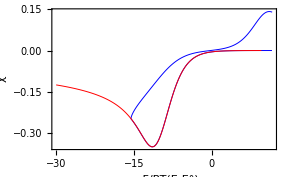

```mathematica
ListPlot[{digiSimData1,result},optionD]
```